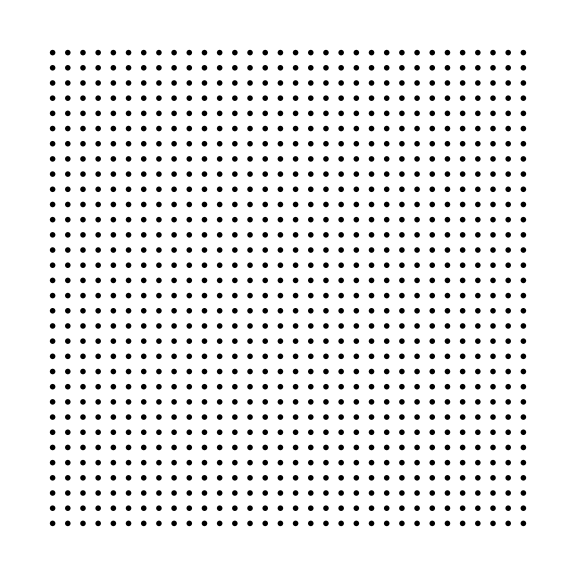

```mathematica
m=31;
n=31;
dx=N[2/m];
dy=N[2/n];
{x,y}=Table[#,{i,-1,1,dx},{j,-1,1,dy}]&/@{j,i};
r=Sqrt[x^2+y^2];
θ=ArcTan[x,y];

k=Sqrt[Pi*n];
J0=BesselJ[0,k*r];
J1=BesselJ[1,k*r]*Exp[I*θ];
{Ex,Ey}=1/Sqrt[2]{{1,1},{I,-I}}.{J0,J1};
EE=Sqrt[Ex*Conjugate[Ex]+Ey*Conjugate[Ey]];
Ex=Ex/EE;
Ey=Ey/EE;

Exx=Ex*Conjugate[Ex];
Eyy=Ey*Conjugate[Ey];
Exy=Ex*Conjugate[Ey];
Is=Re[Exx+Eyy];
Qs=Re[Exx-Eyy];
Us=2Re[Exy];
Vs=-2Im[Exy];

A=(Is+Sqrt[Qs^2+Us^2])/2;
B=(Is-Sqrt[Qs^2+Us^2])/2;
θ=ArcTan[Qs,Us]/2;
H=Sign[Vs];
G=GraphicsGrid[MapThread[Graphics[{RGBColor[(1+#4)/2,0,(1-#4)/2],Rotate[Circle[{0,0},{#1,#2}],#3]}]&,{A,B,θ,H},2]];
Show[G,ImageSize->Large]
```